```mathematica
X={1,1,0,0,0,1,1,2,1,1,1,0,2,2,4,3,2,0,2,2,2,2,3,1,0,2,0,5,3,6,2,1,2,1,8,11,5,8,12,15,22,48,50,73,92,108,113,149,123,97,75,34,6};
n=Length[X];
```

-9.68226+0.312096 t

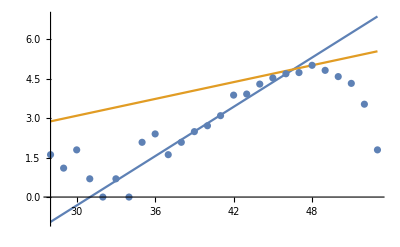

```mathematica
Fit[Table[{k,Log[X[[k]]]},{k,37,48}],{1,t},t]
Show[Plot[{%,(t-1)Log[149]/47},{t,28,n}],ListPlot[Table[{t,Log[X[[t]]]},{t,28,n}]]]
```

```mathematica
A=(Mean[Table[Log[X[[t]]]t,{t,37,48}]]-42.5Mean[Table[Log[X[[t]]],{t,37,48}]])/(Mean[Table[t^2,{t,37,48}]]-42.5^2)
```

0.312096

```mathematica
NSolve[Sum[X[[t]]Exp[a*t]t,{t,48}]/Sum[Exp[2*a*t]t,{t,48}]==Sum[X[[t]]Exp[a*t],{t,48}]/Sum[Exp[2*a*t],{t,48}],a,Reals]
```

NSolve::ivar: 0.224762 is not a valid variable.

NSolve[False,0.224762,Reals]

```mathematica
a=a/.Flatten[NSolve[Sum[X[[t]]Exp[a*t]t,{t,37,48}]/Sum[Exp[2*a*t]t,{t,37,48}]==Sum[X[[t]]Exp[a*t],{t,37,48}]/Sum[Exp[2*a*t],{t,37,48}],a,Reals]]
b=Log[Sum[X[[t]]Exp[a*t]t,{t,37,48}]/Sum[Exp[2*a*t]t,{t,37,48}]]
```

0.224762

-5.75176

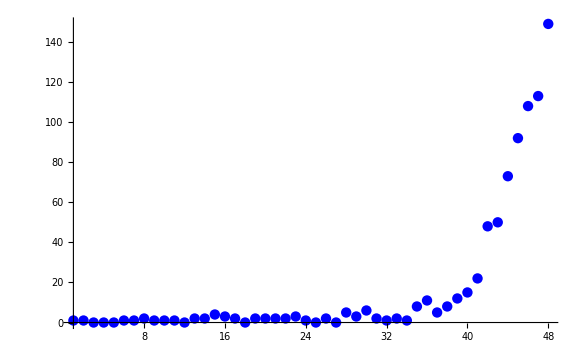

```mathematica
Show[Plot[Exp[a*x+b],{x,1,48}],ListPlot[Table[X[[t]],{t,1,48}],PlotStyle->Blue]]
```

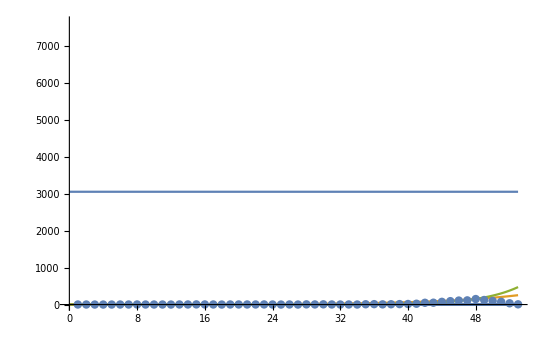

```mathematica
Show[Plot[{Exp[%%%%%%],149^((t-1)/47),Exp[a*t+b]},{t,0,n}],ListPlot[Table[{t,X[[t]]},{t,n}]]]
```

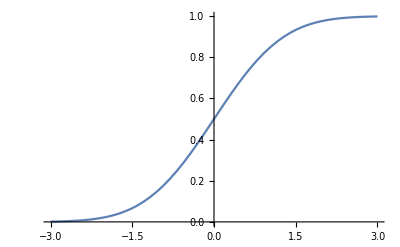

```mathematica
Plot[(1+Erf[Eps/Sqrt[2]])/2,{Eps,-3,3}]
```

```mathematica
D[(1+Erf[Eps/Sqrt[2]])/2,Eps]
```

(ⅇ^(-Eps^2/2))/(√(2 π))

Unset::wrsym: Symbol E is Protected.

```mathematica
Plot[%,{Eps,-3,3}]
```

-Graphics-

```mathematica
Res1=Table[X[[t]]-Exp[a*t+b],{t,32,48}]
```

{-3.22336,-3.28775,-5.62039,-0.288893,0.622099,-7.99339,-8.26805,-8.368,-10.5012,-9.9282,8.0251,-0.0495656,10.3367,13.544,9.77111,-9.98502,-4.9803}

```mathematica
{-3.223355322369165,-3.2877460961505403,-5.620389866148051,-0.2888930714172542,0.6220993418074858,-7.99339020824136,-8.268048294560089,-8.368001812666176,-10.501245775099964,-9.928195120134305,8.025104160803686,-0.04956563757911425,10.336696746207167,13.543982956597276,9.771111787948684,-9.98501559208377,-4.980303915619885}

n1=Length[Res1]
m=Mean[Res1]
s=StandardDeviation[Res1]
```

{-3.22336,-3.28775,-5.62039,-0.288893,0.622099,-7.99339,-8.26805,-8.368,-10.5012,-9.9282,8.0251,-0.0495656,10.3367,13.544,9.77111,-9.98502,-4.9803}

17

-1.77619

```mathematica
Max[Table[k/n1-(Erf[(Sort[Res1][[k]]-m)/s/Sqrt[2]]+1)/2,{k,n1}]];
Max[Table[(Erf[(Sort[Res1][[k]]-m)/s/Sqrt[2]]+1)/2-(k-1)/n1,{k,n1}]];
Dn=Max[%,%%]
Sqrt[n1]Dn
```

0.161387

0.665415